```mathematica
ClearAll["Global`*"]
x=1;
FindRoot[Max[{Exp[x],1}]/((n+1)!) x^(n+1)==10^-16,{n,10}]
N[Sum[x^k/(k!),{k,0,Ceiling[n/.%]}],30]
N[Exp[x],30]
```

{n→17.4933}

2.71828182845904522670811748171

2.71828182845904523536028747135

```mathematica
ClearAll["Global`*"]
f[x_]:=x^3-2 x^2+7x+4;
x0=-1;
x1=1;
a={{x0,f[x0]},{x1,f[x1]}};
For[i=1,i<100,len=Length[a];m=(a[[len,2]]*a[[len-1,1]]-a[[len-1,2]]*a[[len,1]])/(a[[len,2]]-a[[len-1,2]]);
n=f[m];
a=Join[a,{{m,n}}];
If[Abs[n]<10^-16,Break[]]
]
N[a,10]
```

{{-1.,-6.},{1.,10.},{-0.25,2.109375},{-0.5841584158,-0.9709298545},{-0.4788297561,0.07985073926},{-0.4868338736,0.002765300983},{-0.4871210068,-8.220023512×10^-6},{-0.4871201558,8.432000035×10^-10},{-0.4871201559,2.570784177×10^-16},{-0.4871201559,-8.040042319×10^-27}}

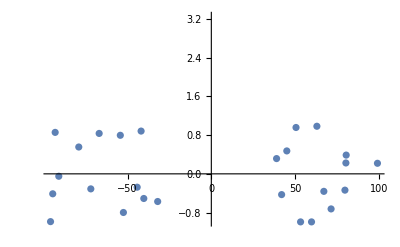

```mathematica
ClearAll["Global`*"]
f[x_]:=Piecewise[{{Sin[x],-100<=x<=-20},{x^2,-20<x<20},{Cos[x],20<=x<=100}}]
a=RandomReal[{-100,100},30];
ListPlot[Table[{a[[k]],f[a[[k]]]},{k,1,30}]]
```

```mathematica
ClearAll["Global`*"]
A=RandomReal[{-10,10},{4,4}];
A//MatrixForm
Eigensystem[A]//TableForm
```

(5.4968 | 9.4981 | 1.75294 | 0.622954
-1.06311 | 9.45223 | 0.00364799 | -4.21326
2.53902 | -8.64863 | -9.88413 | 9.18264
0.882614 | 9.93428 | -6.21885 | -4.12304)

-5.08314+5.3518 ⅈ | -5.08314-5.3518 ⅈ | 5.55407+3.87385 ⅈ | 5.55407-3.87385 ⅈ
0.215941+0.0724674 ⅈ
-0.169827-0.0573624 ⅈ
-0.350804+0.53271 ⅈ
-0.713543+0. ⅈ | 0.215941-0.0724674 ⅈ
-0.169827+0.0573624 ⅈ
-0.350804-0.53271 ⅈ
-0.713543+0. ⅈ | 0.856606+0. ⅈ
-0.0332237+0.33307 ⅈ
0.186857-0.0320298 ⅈ
0.0595176+0.338679 ⅈ | 0.856606+0. ⅈ
-0.0332237-0.33307 ⅈ
0.186857+0.0320298 ⅈ
0.0595176-0.338679 ⅈ

```mathematica
ClearAll["Global`*"]
A=RandomReal[{-10,10},{4,4}];
A//MatrixForm
Sqrt[Max[Abs[Eigenvalues[Transpose[A].A]]]]
```

(5.79674 | 9.38046 | -9.9343 | -2.22731
3.52567 | 8.18089 | 9.59397 | 6.07595
6.5077 | -5.06366 | -5.54638 | -2.65729
-2.85535 | -5.64692 | 3.70188 | 9.55255)

18.9307

```mathematica
ClearAll["Global`*"]
f[n_]:=Module[{A},A=ConstantArray["*",{n,n}];
For[i=2,i<=n-1,i++,
A[[2,i]]=0;
A[[i,2]]=0;
A[[n-1,i]]=0;
A[[i,n-1]]=0;
];A]
f[5]//MatrixForm
f[6]//MatrixForm
```

(* | * | * | * | *
* | 0 | 0 | 0 | *
* | 0 | * | 0 | *
* | 0 | 0 | 0 | *
* | * | * | * | *)

(* | * | * | * | * | *
* | 0 | 0 | 0 | 0 | *
* | 0 | * | * | 0 | *
* | 0 | * | * | 0 | *
* | 0 | 0 | 0 | 0 | *
* | * | * | * | * | *)

```mathematica
BeginPackage["Global`"];

Norm1::usage="计算矩阵的1范数";

NormInf::usage="计算矩阵的∞范数";

Norm1[x_]:=Module[{n},n=Dimensions[x][[2]];
Max[Table[Total[Abs[x[[All,j]]]],{j,1,n}]]];

NormInf[x_]:=Module[{m},m=Dimensions[x][[1]];
Max[Table[Total[Abs[x[[i,All]]]],{i,1,m}]]];

EndPackage[];
```

```mathematica
Clear[A];
A=RandomReal[{-10,10},{4,4}];
A//MatrixForm
{Norm1[A],NormInf[A]}
```

(-8.44667 | -6.17765 | 8.45907 | -9.9968
0.404274 | -5.65163 | -6.40588 | -0.010263
-5.5465 | 8.96117 | -8.07383 | -1.28022
-5.91437 | -2.95136 | -3.97416 | 6.1531)

{26.9129,33.0802}